# Clojure Analysis

```mathematica
Quit
```

```mathematica
Needs["AssociativeUtils`"]
```

Basically a big map-reduce. Like everything.

## Utils

### General Predicates

```mathematica
notFalseQ[x_] := !(x  === False)
```

```mathematica
everyQ[pred_, xs_] := 
Module[{sentinel},
Catch[
Fold[
If[pred[#2], True, Throw[False, sentinel]]&,
True,
xs],
sentinel]]
```

```mathematica
thingQ[]:= False
```

```mathematica
thingQ[__]:= True
```

### let

```mathematica
Clear[let]
```

```mathematica
SetAttributes[let, HoldAll]
```

```mathematica
let[{HoldPattern[Set[lhs_ , rhs_]], rst___}, body___] :=
With[{lhs = rhs},
let[{rst}, body]]
```

```mathematica
let[{}, body___] := body
```

```mathematica
let[{a=b,c=a}, c]
```

b

### cons car cdr, motherfuckers

```mathematica
ClearAll[cons,car,cdr]
```

```mathematica
cons[x_, ys_]:= Prepend[ys, x]
```

```mathematica
cons[x_, Null]:= {x}
```

```mathematica
car[_[x_, ___]]:= x
```

```mathematica
car[_[]|Null]:= Null
```

```mathematica
cdr[h_[_, xs___]]:= h[xs]
```

```mathematica
cdr[h_[]]:= Null
```

### repeatedly

```mathematica
ClearAll[repeatedly]
```

```mathematica
repeatedly[f_, args___, n_]:=Reap[Do[Sow[f[args]],{n}]]⟦2,1⟧
```

```mathematica
repeatedly[f_, args___, 0]:= {}
```

### Other Shit

```mathematica
qwikCases[expr_, frm_]:=Cases[expr, frm, ∞, Heads-> True]
```

```mathematica
qwikPartition[x_,n_,off_]:=Partition[x,n,off,{1,1},{}]
```

```mathematica
qwikPartition[x_, n_]:= qwikPartition[x,n,n]
```

```mathematica
columnate[x_, rows_]:= Partition[x,rows,rows,{1,1},{Null}]//Transpose
```

### Testing

Dependency-free (associative utils may help construct test batteries, though).

```mathematica
ClearAll[testWalk,runTests, is, notFound,passed,failed];Attributes[is]= {HoldAll};
```

```mathematica
testWalk[tests_,behind_, ahead_ ]:= 
testWalk[First[ahead]/.Append[tests, _ :> Throw[notFound["behind"->behind, "ahead"-> ahead ]]], Append[behind, First[ahead]], Rest[ahead]]
```

```mathematica
testWalk[tests_, behind_, {}]:= testWalk[#,behind,{}]&/@tests
```

```mathematica
testWalk[r_ -> m_, behind_, {}]:=testWalk[m, Append[behind, r], {}]
```

```mathematica
testWalk[isForm_is, behind_, {}]:=
If[(SameQ@@isForm),
passed["path"->behind,Replace[isForm, is[xs___]:> Hold[SameQ[xs]]]],
failed["path"->behind, "expected"->Replace[isForm, is[xs___]:> Hold[SameQ[xs]]], "got"-> Replace[isForm, is[xs___]:> SameQ@@@Hold@@{{xs}}]]]
```

```mathematica
runTests[tests_,path:{___String}]:=Flatten@testWalk[tests,{},path]
```

```mathematica
runTests[tests_]:= runTests[tests, {}]
```

### Mapper

```mathematica
mapper[f_]:= Map[f,#]&
```

### asMap

```mathematica
asMap[x_]:= lookup[x,##]&
```

```mathematica
asMap[x_, default_]:= 
Replace[{##},
{{k_}:>lookup[x,k, default],
_:> lookup[x, ##]}]&
```

```mathematica
runTests[
let[
{m1 = someStructure["a"-> "A"]},
{is[asMap[m1]["a"],"A"],
is[asMap[m1,"C"]["c"], "C"],
is[asMap[m1]["b", "C"],"C"]}]]
```

{passed[path→{},Hold[asMap[someStructure[a→A]][a]===A]],passed[path→{},Hold[asMap[someStructure[a→A],C][c]===C]],passed[path→{},Hold[asMap[someStructure[a→A]][b,C]===C]]}

### qwikReap

```mathematica
Attributes[qwikReap]= HoldAll;
```

```mathematica
qwikReap[expr_]:=Replace[Reap[expr]⟦2⟧, {x_}:> x]
```

### graphUnion2

```mathematica
ClearAll[graphUnion2]
```

```mathematica
graphUnion2[]:=Graph[{}]
```

```mathematica
graphUnion2[g_Graph]:=g
```

```mathematica
graphUnion2[gs__Graph]:=GraphUnion[gs]
```

### qwikMapIndexed

Like mapIndexed, but just maps over first level and passes in unwrapped index.

```mathematica
qwikMapIndexed[f_,expr_]:=MapIndexed[f[#1,#2⟦1⟧]&, expr]
```

### stringishQ

```mathematica
stringishQ[_]:= False
```

```mathematica
stringishQ[String_|StringExpression_]:= True
```

### compBy

```mathematica
compBy[f_,comp_, xs_List]:=
Replace[
Fold[
{bldg,x}↦
let[{xn=f[x]},
Replace[bldg,
{{prevval_, prevn_}:> If[comp[xn,prevn],{x,xn},bldg],
_ :> {x,xn}}]],
Null,
xs],
{val_,_}:> val]
```

```mathematica
maxBy[f_,xs_List]:= compBy[f,Greater,xs]
```

```mathematica
minBy[f_,xs_List]:=compBy[f,Less,xs]
```

## (more) Graph Utils

### edgeyQ

```mathematica
edgeyQ[_DirectedEdge|_UndirectedEdge|_Rule]:=True
```

```mathematica
edgeyQ[_]:=False
```

### set graph things

```mathematica
ClearAll[setGraphOpts,setGraphVerts,setGraphEdges,addGraphOpts,mapToGraphVerts]
```

```mathematica
setGraphOpts[g_Graph, opts:OptionsPattern[Graph]]:=Graph[VertexList@g,EdgeList@g, opts]
```

```mathematica
setGraphVerts[g_Graph,verts_]:= Graph[verts,EdgeList[g],Options[g]]
```

```mathematica
setGraphEdges[g_Graph,edges_]:=
 Graph[VertexList[g], edges, Options[g]]
```

```mathematica
addGraphOpts[g_Graph, opts:OptionsPattern[Graph]]:=
With[{opts2 =Join[{opts}, {Options[g]}]},
Graph[VertexList@g,EdgeList@g, 
Sequence@@ opts2]]
```

```mathematica
Options@Graph[{a->b}, EdgeLabels-> {(a->b)->"bla"}]
```

{EdgeLabels→{a->b→bla}}

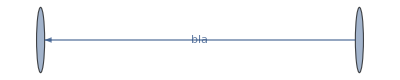

```mathematica
Graph[{a->b}, EdgeLabels-> {(a->b)->"bla"}]
```

```mathematica
Options[Graph[{a->b}, EdgeLabels-> {(a->b)->"bla"}]]
```

{EdgeLabels→{a->b→bla}}

### get graph things

```mathematica
getEdgeLabels[g_Graph]:=EdgeLabels/.Append[Options[g],_-> {}]
```

```mathematica
getVertexStyle[g_Graph]:= VertexStyle/.Append[Options[g],_-> {}]
```

Not sure if this is quite right, that is, maybe there’s a difference between having the empty list set as a vertex’s style and excluding it from the style thing altogether:

```mathematica
getVertexStyle[g_Graph, v_]/;VertexQ[g,v]:= v/.Append[getVertexStyle[g], _->{}]
```

### mapToGraphVerts, mapToGraphEdges

```mathematica
ClearAll[mapToGraphVerts,mapToGraphEdges]
```

```mathematica
mapToGraphVerts[f_,g_Graph]:= 
let[
{vs1=VertexList@g,
vs2=f/@vs1,
rs=Thread[vs1-> vs2],
es=EdgeList@g,
es2=(Replace[#,rs,{1}]&)/@es,
ers=Thread[es->es2]},
Graph[vs2,
es2,
Sequence@@(Options[g]/.ers)]]
```

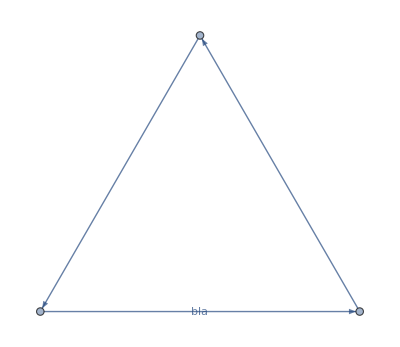

```mathematica
let[
{g=Graph[{a->b,b->c,c->a}, EdgeLabels->{(a->b)-> "bla"}]},
mapToGraphVerts[foo,g]]
```

```mathematica
mapToGraphEdges[f_,g_Graph]:= setGraphEdges[g, f/@EdgeList[g]]
```

### decoration conveniences

```mathematica
addToolTips[g_Graph]:=setGraphVerts[g,Tooltip/@VertexList[g]]
```

```mathematica
addNameLabels[g_Graph]:= addGraphOpts[g, VertexLabels-> "Name"]
```

```mathematica
addEdgeToolTips[g_Graph]:=
let[{els=getEdgeLabels[g]},
Switch[els,
Automatic,setGraphEdges[g,Tooltip[#,#]&/@EdgeList[g]],
_,
let[
{tts=
Append[
Replace[els,(e_ -> l_):> (e-> Tooltip[e,l]),{1}],
e_:> Tooltip[e,e]]},
setGraphEdges[g,Replace[EdgeList@g, tts,{1}]]]]]
```

```mathematica
ornament[g_Graph]:= addEdgeToolTips@addToolTips@addNameLabels@g
```

### selfLoops, removeSelfLoops

```mathematica
ClearAll[selfLoops,removeSelfLoops]
```

```mathematica
selfLoops[g_Graph]:=Cases[EdgeList[g],_[x_,x_]]
```

```mathematica
removeSelfLoops[g_Graph]:= EdgeDelete[g,selfLoops[g]]
```

### singleEdgify

```mathematica
ClearAll[singleEdgify,edgeListTransform]
```

```mathematica
edgeListTransform[el_List,v:( Automatic|True|False)]:=
Switch[v,
Automatic, el,
True,Replace[el,UndirectedEdge->DirectedEdge,{2},Heads-> True],
False, Replace[el, DirectedEdge-> UndirectedEdge,{2}, Heads-> True]]
```

```mathematica
edgeListTransform[Null, _]:= Null
```

```mathematica
Options[singleEdgify]= {DirectedEdges-> Automatic,allowSelfLoops-> False}
```

{DirectedEdges→Automatic,allowSelfLoops→False}

```mathematica
singleEdgify[el_List,OptionsPattern[singleEdgify]]:=
With[
{searcher = 
If[OptionValue[allowSelfLoops],
Identity,
#|Reverse@#&]},
edgeListTransform[#, OptionValue[DirectedEdges]]&@
If[Length[el]<2,
el,
Reap[
NestWhile[
Function[ahd,
With[{e= First[ahd]},
Sow[e];
DeleteCases[Rest@ahd,searcher@e]]],
el,
#≠{}&]]⟦2,1⟧]]
```

```mathematica
singleEdgify[g_Graph,opts:OptionsPattern[singleEdgify]]:= setGraphEdges[g,singleEdgify[EdgeList[g],opts]]
```

### extractVertexCoordinates

```mathematica
ClearAll[extractVertexCoordinates, extractVertexCoordinateRules,extractGraphPlotCoordinates,overlaySubgraph]
```

```mathematica
extractGraphPlotCoordinates[Graphics[Annotation[_,VertexCoordinateRules-> vcr_],___]]:=vcr
```

```mathematica
extractVertexCoordinates[g_Graph]:=
VertexCoordinates/.AbsoluteOptions[g, VertexCoordinates]
```

```mathematica
extractVertexCoordinates[g_Graphics]:=extractGraphPlotCoordinates@g
```

```mathematica
extractVertexCoordinates[g_Graph, verts_List]:=
verts/.Thread[VertexList@g-> extractVertexCoordinates@g]
```

```mathematica
extractVertexCoordinateRules[g_Graph]:=
Thread[VertexList[g]->extractVertexCoordinates[g]]
```

```mathematica
overlaySubgraph[g_Graph,sg_Graph]:=
Show[g,
addGraphOpts[sg,
VertexCoordinates-> 
(VertexList[sg]/.extractVertexCoordinateRules[g])]]
```

### toGraph

```mathematica
ClearAll[toGraph]
```

Not sure what the point of this is, whatever

```mathematica
toGraph[xs___]:=Graph[xs]
```

```mathematica
toGraph[g_Graph]:= g
```

```mathematica
toGraph[Null]:=Graph[{}]
```

### nullGraphQ

```mathematica
nullGraphQ[_]:= False
```

```mathematica
nullGraphQ[g_Graph]:= VertexList[g]=={}
```

### fix ReverseGraph

Note: unprotecting graph. Deal with it.

```mathematica
Unprotect[Graph];
```

```mathematica
Graph/: ReverseGraph[g_Graph?nullGraphQ]:=g
```

TagSetDelayed::write: Tag Graph in ReverseGraph[g_Graph ? nullGraphQ] is Protected.

$Failed

### edgeAdd2

I HATE this shit. VertexAdd behaves correctly, so it’s just stupid inconsistent bullshit.

```mathematica
ClearAll[edgeAdd2]
```

```mathematica
edgeAdd2[g_Graph,e:Except[_List]]/;¬EdgeQ[g,e]:=EdgeAdd[g,e]
```

```mathematica
edgeAdd2[g_Graph,es_List]:= Fold[edgeAdd2,g,es]
```

```mathematica
edgeAdd2[g_Graph,___]:= g
```

### directedNeighborhoodGraph, upstreamDirectedNeighborhoodGraph

```mathematica
ClearAll[directedNeighborhoodGraph,upstreamDirectedNeighborhoodGraph,edgeyQ]
```

Replace this with something using nestwhile and a good test using the previous value so we can stop running when the graph hits a fixpoint, not just the lump of state we’re whaling on. That way we can specify ∞ n’s, for example.

```mathematica
directedNeighborhoodGraph[g_?DirectedGraphQ,vs_List,n_]:=
First[
FixedPoint[
bldg↦
Replace[bldg,
{{g,___}:> bldg,
{prevg_,prevvs_/;prevvs≠{},level_/;level<n}:> 
(Join@@ (Cases[IncidenceList[g,#],_[#,_]]&/@prevvs)/.
{{}|{{}}:> {prevg,{},level+1},
newEs_:>{edgeAdd2[prevg,newEs],newEs⟦;;,2⟧,level+1}})}],
{Graph[{}],vs,0}]]
```

```mathematica
directedNeighborhoodGraph[g_?DirectedGraphQ,v_,n_]:=directedNeighborhoodGraph[g,{v},n]
```

```mathematica
directedNeighborhoodGraph[g_Graph,v_]:=directedNeighborhoodGraph[g,v,1]
```

```mathematica
directedNeighborhoodGraph[args___]:=NeighborhoodGraph[args]
```

```mathematica
upstreamDirectedNeighborhoodGraph[g_Graph,args___]:=ReverseGraph[directedNeighborhoodGraph[ReverseGraph[g],args]]
```

### getATree, getADag

```mathematica
ClearAll[getATree,getADag]
```

```mathematica
Options[getATree]={DirectedEdges-> Automatic};
```

```mathematica
getATree[g_Graph, v_, OptionsPattern[getATree]]:=
edgeListTransform[#,OptionValue[DirectedEdges]]&@
car@car@cdr@Reap[
Module[{cur=v},
BreadthFirstScan[g,v,
{"PrevisitVertex"-> (Set[cur,#]&),
"FrontierEdge"-> (Sow[#/.e_[as___, cur, bs___]:>e[cur,as,bs] ]&)}]]]
```

Note that DirectedEdge can actually take more than two arguments:

```mathematica
DirectedEdge[a,b,c,d,e]
```

```mathematica
getADag[g_Graph,v_, OptionsPattern[getADag]]:=
Reap[
Module[{cur=v},
BreadthFirstScan[g,v,
With[{edgeHandler=Sow[#/._[as___, cur, bs___]:>DirectedEdge[cur,as,bs] ]&},
{"PrevisitVertex"-> (Set[cur,#]&),
"FrontierEdge"-> edgeHandler,
"CycleEdge"-> edgeHandler}]]]]//
cdr//car//car//Replace[#,Null-> {}]&
```

### upstreamGraph, downstreamGraph, highlightWithNeighborhood

```mathematica
ClearAll[upstreamGraph,downstreamGraph]
```

```mathematica
upstreamGraph[g_Graph,v_]/;VertexQ[g,v]:=
getADag[ReverseGraph[g],v]//toGraph//ReverseGraph//HighlightGraph[#,v]&//ornament
```

```mathematica
upstreamGraph[g_Graph,vs_List]:=
HighlightGraph[
Apply[graphUnion2,
(v↦getADag[ReverseGraph[g],v]//toGraph//ReverseGraph)/@vs],
vs]
```

```mathematica
downstreamGraph[g_Graph, v_]/;VertexQ[g,v]:=getADag[g,v]//toGraph//HighlightGraph[#,v]&//ornament
```

```mathematica
downstreamGraph[g_Graph,vs_List]:=
HighlightGraph[
Apply[graphUnion2,
(v↦getADag[g,v]//toGraph)/@vs],
vs]
```

Differentiated from NeighborhoodGraph:

```mathematica
highlightWithNeighborhood[g_Graph, vs_, n_]:= NeighborhoodGraph[g,vs,n]//HighlightGraph[#,vs]&//ornament
```

```mathematica
highlightWithNeighborhood[g_Graph, vs_]:= highlightWithNeighborhood[g,vs,1]
```

### qwik highlighting etc tools

```mathematica
ClearAll[hlNeighborhood,hlUpstream,hlDownstream]
```

```mathematica
hlNeighborhood[g_Graph, vs_List, n_]:= NeighborhoodGraph[g,vs,n]//HighlightGraph[g,(Style[#,Red]&)/@vs]&
```

```mathematica
hlNeighborhood[g_Graph, vs_List]:= hlNeighborhood[g,vs,1]
```

```mathematica
hlUpstream[g_Graph,v_]:=HighlightGraph[g,downstreamGraph[g,v]]
```

```mathematica
hlDownstream[g_Graph,v_]:=HighlightGraph[g,downstreamGraph[g,v]]
```

```mathematica
RGBColor[.2,.6,.5,1]
```

-Graphics-

```mathematica
hlUpDown[g_Graph,v_]:=
let[
{up=upstreamGraph[g,v],
down=downstreamGraph[g,v],
intersect= GraphIntersection[up,down]//EdgeList//Graph},
HighlightGraph[g,
{Style[v,Yellow],
Style[intersect,RGBColor@@({.5,.2,.6}*1.5)],
Style[down, Darker@Green],
Style[up,Darker@ Red]}]//ornament]
```

## Init

Looks like if we dropped clojure-1.5.1.jar rather than clojure-1.2.0.jar into lib we mux up JLink. Should probably get the latest version of JLink.jar, or something. Ideally we could get it from some repo and handle this via Leiningen.

### load

```mathematica
AppendTo[$Path,"/Users/timothygardner/code/ClojureLink/src/mathematica"];
```

```mathematica
Needs["ClojureLink`"]
```

```mathematica
InstallClojureLink["/Users/timothygardner/code/ClojureLink",
{"/Users/timothygardner/code/ClojureLink/src/clj"}];
```

```mathematica
SetClojureLinkAutoReplacements[EvaluationNotebook[]]
```

### qmark

Actually this is a bug. Totally doesn’t work, play around with question marks to see how

```mathematica
qmark="⁇"
```

⁇

```mathematica
addQmark[s_String]:= s<>qmark
```

```mathematica
addQmark[s_Symbol]:= Symbol@addQmark@ToString@s
```

### does it float

```mathematica
ClojureEvaluate[
with‑out‑str[
print@eval@load‑string@"*clojure-version*"]]
```

{:qualifier nil, :minor 5, :incremental 1, :major 1}

## Namespaces

### Problem

in-ns doesn’t work, getting it to work would require rewriting the clojure side of ClojureLink somewhat.

```mathematica
currentNamespace[]:=ClojureEvaluate[with‑out‑str[print[load‑string["*ns*"]]]]
```

```mathematica
currentNamespace[]
```

#<Namespace user>

```mathematica
coreSymbol= ClojureSymbol@"ClojureLink.core"
```

ClojureSymbol[ClojureLink.core]

```mathematica
ClojureEvaluate[in‑ns@quote@coreSymbol]
```

«JavaObject[clojure.lang.Namespace]»

```mathematica
currentNamespace[]
```

#<Namespace user>

```mathematica
ClojureEvaluate[in‑ns@quote@ClojureSymbol["clojure.tools.analyzer"]]
```

«JavaObject[clojure.lang.Namespace]»

```mathematica
currentNamespace[]
```

#<Namespace user>

```mathematica
ClojureEvaluate[require[quote@coreSymbol]]
```

```mathematica
analysisSymbol = ClojureSymbol@"ClojureLink.analysis"
```

ClojureSymbol[ClojureLink.analysis]

```mathematica
ClojureEvaluate[require[quote[analysisSymbol]]]
```

```mathematica
ClojureEvaluate[in‑ns[quote[analysisSymbol]]]
```

«JavaObject[clojure.lang.Namespace]»

```mathematica
currentNamespace[]
```

#<Namespace user>

### Work-around

Use: nsreq["ClojureLink.analysis"];nsreq["clojure.jvm.tools.analyzer"];

```mathematica
nsreq[ns_ClojureSymbol]:=ClojureEvaluate@require@quote@ns
```

```mathematica
nsreq[ns_String]:= nsreq[ClojureSymbol[ns]]
```

```mathematica
nsq[ns_, x_]:= ClojureSymbol[StringJoin@@({ns,"/",x}/.ClojureSymbol[y_]:> y)]
```

## Parse Project

Just whack it with the predefined instaparse thing (for all its many warts)

```mathematica
nsreq["ClojureLink.parser"];
```

```mathematica
ClearAll[parseFile,parseString];
```

```mathematica
parseFile[f_String]:= ClojureEvaluate[ClojureLink․parser`parse‑clojure‑file[f]]
```

```mathematica
parseFile[f_String, start_]:=ClojureEvaluate[ClojureLink․parser`parse‑clojure‑file[f, start]]
```

```mathematica
parseFile[f_String, start_,end_]:=ClojureEvaluate[ClojureLink․parser`parse‑clojure‑file[f, start,end]]
```

```mathematica
parseString[s_String]:= ClojureEvaluate[ClojureLink․parser`parse‑clojure‑string[s]]
```

Extend this for ClojureScript & whatever

```mathematica
clojureFiles[path_String]:=FileNames[__~~(".clj"|".cljs"),path,∞]
```

```mathematica
parseProject[path_String]:=ClojureEvaluate[ClojureLink․parser`parse‑clojure‑files@@clojureFiles[path]]
```

### Tests

```mathematica
parseProjectTest=
{is[True,MatchQ[parseString["[bla]"], {։top,{։vector,{։symbol,"bla"}}}]],
is[True, MatchQ[parseFile["/Users/timothygardner/code/mathematica-clojure-analysis/clj-test-project/src/clj_test_project/core.clj"],_List]]};
```

```mathematica
runTests[parseProjectTest]
```

{passed[path→{},Hold[True===MatchQ[parseString[[bla]],{։top,{։vector,{։symbol,bla}}}]]],passed[path→{},Hold[True===MatchQ[parseFile[/Users/timothygardner/code/mathematica-clojure-analysis/clj-test-project/src/clj_test_project/core.clj],_List]]]}

## AST Reference Graph

### basic grammar patterns

```mathematica
whitespaceP= {։whitespace, ___};
```

### symb, keyword

```mathematica
stringify[symb[s_String]]:=s
```

```mathematica
stringify[symb[ns_String,s_String ]]:=ns<>"/"<>s
```

```mathematica
stringify[keyword[s_String]]:=":"<>s
```

```mathematica
stringify[keyword[ns_String,s_String]]:= ":"<>ns<>"/"<>s
```

```mathematica
cljname[s_symb]:= stringify[s]
```

```mathematica
cljname[keyword[s_String]]:=s
```

```mathematica
cljname[keyword[ns_String,s_Str]]:=s
```

### nodify

```mathematica
nsPrefixSplit[s_String]:= StringSplit[s,"/"]
```

```mathematica
nsPrefixSplit["/"]:={"/"}
```

```mathematica
defStringPatterns={"def"~~___};
```

```mathematica
metaSeqP=PatternSequence[{։metadata‑caret, _}, _];
```

```mathematica
nodifyRules=
{whitespaceP:> Sequence[],
{։symbol, n_String} :>symb@@nsPrefixSplit[n], (*note this doesn't cover clr-type expressions yet*)
{։keyword, s_String}:> 
First[
StringCases[s,colon:(":"..)~~rst__:> 
Switch[colon,
":", keyword@@nsPrefixSplit[rst],
"::",keyword[":",rst]]]],
Sequence@@
Map[
Function[{pfn},
listForm[s_symb/; StringMatchQ[stringify[s],pfn], mfs___metaForm,n_symb, body___]:> 
definingForm["type"-> stringify[s], "definiendum"-> n, "body"->{body}, "metadata"-> {mfs}]],
defStringPatterns],
Sequence@@
Table[
spec/.{tag_,typ_ }:> 
({tag,body___}:> 
typ@@Cases[{body}, Except[whitespaceP]]),
{spec, 
{{։vector, vectorForm},
{։list, listForm},
{։map, mapForm},
{։set, setForm}}}],
(*not at all sure about this next bit. see eg core_deftype.clj for motivation*)
listForm[symb["in-ns"],___,nm_symb]:> 
nsForm[
"namespaceName" -> nm,
"body" -> {}],
listForm[symb["ns"], ___,nm_symb, body___]:>
nsForm[
"namespaceName"-> nm,
"body"-> {body}],
h:_[as___,m:metaSeqP,bs___]:> 
Head[h]@@{as,Rest@metaForm[m],bs}};
```

Seems we have to break the following out to deal with some evaluation order weirdness. Also less ugly this way.

```mathematica
listOrVectorHP=listForm|vectorForm;
```

```mathematica
ClearAll[dotJoin]
```

```mathematica
dotJoin[symb[a_], symb[b_]]:= symb[a<>"."<>b]
```

Tip o the day: consider breaking rule lists used in RewriteRepeated into chain of RewriteRepeated calls on single rules. Much easier to reason about.

```mathematica
refineRequire[listOrVectorHP[keyword["require"],body___]]:=
{body}/.
{listOrVectorHP[x_symb]:> requireForm[x],
listOrVectorHP[x_symb, keyword["as"], a_symb]:> requireForm[x,keyword["as"], a]}//.
listOrVectorHP[x_symb,ys__]:>Replace[{ys},{y_symb:> requireForm[x, y], y_requireForm:> Prepend[y,x]},{1}]//.requireForm[x_symb, y_symb, rst___]:> requireForm[dotJoin[x,y], rst]
```

```mathematica
refineNsForms[x_]:=
x/.nsf_nsForm:> 
Replace[nsf,
("body"-> b_):> 
("requireForms"-> 
(Flatten@Cases[b, r:listOrVectorHP[keyword["require"], ___]:> refineRequire[r]])),
{1}]
```

```mathematica
nodify[x_]:= x//.nodifyRules//refineNsForms
```

### definingForm

```mathematica
getDefiniendum[df_definingForm]:= lookup[df, "definiendum"]
```

```mathematica
getBody[df_definingForm]:= lookup[df, "body"]
```

### nsData

```mathematica
topDefs[nsd_nsData]:=lookup[nsd,"topDefs"]
```

#### toNsData

```mathematica
defsByNamespace[asts_List]:= 
groupBy[
qwikReap[
Fold[
Function[{ns, x},
If[MatchQ[x, _nsForm],
x,
Sow[{ns,x}];ns]],
"user",
Cases[asts,(_nsForm|_definingForm) ,∞]]],
First]/.
(lhs_ -> rhs_):> (lhs-> rhs⟦;;,2⟧)
```

Extend the following to deal with “user” case when we know more about nsForms:

```mathematica
toNsData[asts_List]:=
defsByNamespace[asts]/.
{(lhs_-> rhs_):>nsData["nsForm"-> lhs,"topDefs"-> rhs]}
```

```mathematica
getNamespaceName[nsf_nsForm]:=lookup[nsf, "namespaceName"]
```

```mathematica
getNamespaceName[nsdt_nsData]:= getNamespaceName[lookup[nsdt, "nsForm"]]
```

### expandVars

#### expandIntranamespaceVars

```mathematica
varMap[nsd_nsData]:=
With[{ns=First@getNamespaceName[nsd]},
(#/.s:symb[v_]:>(s-> symb[ns, v])&)/@getDefiniendum/@lookup[nsd,"topDefs"]]
```

```mathematica
expandIntranamespaceVars[nsds:{___nsData}]:=
Map[
Function[nsd,
update[nsd, "topDefs", #/.varMap[nsd]&]],
nsds]
```

#### expandAliasedVars

```mathematica
ClearAll[expandAliasedVars]
```

```mathematica
aliasMap[nsd_nsData]:=
qwikCases[
lookupIn[nsd, {"nsForm", "requireForms"}],
requireForm[ns_symb, keyword["as"], a_symb]:> (a-> ns)]
```

```mathematica
aliasVarMap[nsd_nsData]:=
aliasMap[nsd]/.(symb[a_] -> symb[ns_]):>(symb[a, nm_]:> symb[ns, nm])
```

```mathematica
expandAliasedVars[nsds:{___nsData}]:= 
Map[
Function[nsd,
update[nsd, "topDefs", #/.aliasVarMap[nsd]&]],
nsds]
```

#### expandVars

```mathematica
expandVars[nsds:{___nsData}]:=nsds//expandAliasedVars//expandIntranamespaceVars
```

### expandKeywords

```mathematica
expandKeywords[nsd_nsData]:=
let[{ns=First@getNamespaceName[nsd]},
update[nsd,"topDefs",#/.keyword[":",bla_]:> keyword[ns,bla]&]]
```

```mathematica
expandKeywords[nsds:{___nsData}]:=expandKeywords/@nsds
```

### nsGraph

```mathematica
defrefs[df_definingForm]:=
qwikCases[
getBody[df],
s:symb[_,_]:>stringify[s]]
```

```mathematica
defGraph[df_definingForm]:=
With[{d=stringify[getDefiniendum[df]]},
Graph[{d},Union[(d->#&)/@defrefs[df]]]]
```

```mathematica
nsGraph[nsdt_nsData]:=graphUnion2 @@(defGraph/@topDefs[nsdt])
```

```mathematica
nsGraph[nsdts:{___nsData}]:=graphUnion2 @@(nsGraph/@nsdts)
```

### graphProject

```mathematica
graphProject[asts_List]:= asts//nodify//toNsData//expandVars//expandKeywords//nsGraph
```

```mathematica
graphProject[projectPath_String]:= projectPath//parseProject//graphProject
```

```mathematica
graphFile[f_String]:= f//parseFile//List//graphProject
```

## Review & Todo

This file could be much shorter, and would have been faster to write, if the parse tree had been more to the point originally. We definitely want to nodify, but the rules could have been much simpler, it seems to me. (Maybe not.)

We also lost a fair amount of time dithering over the correct representation, and whether it makes sense to nodify things or just recalculate using some globally defined patterns without modifying the tree at all. The later course of action proved intractably cumbersome with no clear advantages other than an appeal to knee-jerk conservatism, stupid in the presence of immutability.

We’ll want some way to tag vars we’re graphing with their general type (defrecord, defprotcol, multimethod, function, just a thing, etc). Also need some treatment for more subtle defining forms like multimethods, protocols, etc.

Also “projectGraph” would be a better name than “graphProject.”

## Smush

### Namespace Communities

```mathematica
getNamespaceName[s_String]:=StringCases[s,{ns__~~"/"~~__:> ns, _-> Null}]//First
```

```mathematica
varsByNamespace[g_Graph]:=groupBy[VertexList[g],getNamespaceName]
```

```mathematica
namespaceCommunities[g_Graph]:= varsByNamespace[g]/. (ns_ -> vs_):> Labeled[vs,ns]
```

Could make this subtler to preserve other styles, if it becomes an issue:

```mathematica
colorVertsByNamespace[g_Graph]:= 
let[
{vbn=SortBy[varsByNamespace[g], First],
cf=ColorData[{"DarkRainbow","Reverse"}]},
addGraphOpts[
g,
VertexStyle->
Flatten[
qwikMapIndexed[
Function[{nsv,i},
nsv/.(ns_-> vs_):> 
With[{c=cf[i/Length[vbn]]},Replace[vs, v_ :> (v->c),{1}]]],
vbn]]]]
```

### Unqualified Names

```mathematica
unqualifiedName[s_String]:= StringReplace[s,__~~"/"~~n__:> n]
```

```mathematica
unqualifiedName[x_]:=x
```

```mathematica
addUnqualifiedNameLabels[g_Graph]:=addGraphOpts[g, VertexLabels->(#-> unqualifiedName[#]&/@VertexList[g])]
```

### Glam

```mathematica
ornamentProject[g_Graph]:= g//ornament//colorVertsByNamespace//addUnqualifiedNameLabels
```

### Vertex nabbing

```mathematica
vertSelect[g_Graph, pred_]:=Select[VertexList@g,pred]
```

```mathematica
vertCases[g_Graph,p_]:= Cases[VertexList@g,p]
```

```mathematica
vertStringMatches[g_Graph, p_]:= vertSelect[g, x↦(StringQ[x]∧ StringMatchQ[x,p])]
```

```mathematica
vertStringMatches[g_Graph, ps_List]:=
Join@@(vertStringMatches[g,#]&/@ps)
```

### Edge Nabbing

```mathematica
edgeStringMatches[g_Graph, p1_, p2_]:= Cases[EdgeList[g],_[l_,r_]/;(StringMatchQ[l,p1]∧StringMatchQ[r,p2])]
```

### Component Nabbing

```mathematica
componentWithVertex[g_Graph, vs_List]:= Subgraph[g, WeaklyConnectedComponents[g,vs]]
```

### CLR stuff

```mathematica
removeProbableCLRStatics[g_Graph]:=
VertexDelete[g,vertStringMatches[g,RegularExpression["[A-Z].*/.*"]]]
```

### Sloppy

```mathematica
patternForSubstring[s_String]:= ___~~s~~___
```

```mathematica
pfs=patternForSubstring;
```

```mathematica
regex=RegularExpression;
```

```mathematica
rpclrs=removeProbableCLRStatics;
```

```mathematica
vsm=vertStringMatches;
```

```mathematica
dsg=downstreamGraph;
```

```mathematica
usg=upstreamGraph;
```

```mathematica
sloppyEdgeAdd[g_Graph, es_List]:=
EdgeAdd[g,Flatten[Tuples/@Replace[es,x_:> vsm[g,x],{2}]]]
```

```mathematica
sloppyEdgeDelete[g_Graph, es_List]:=
EdgeDelete[g,qwikCases[edgeStringMatches[g,##]&@@@es,_DirectedEdge]]
```

```mathematica
sloppyVertexDelete[g_Graph,es_List]:=VertexDelete[g,DeleteDuplicates@Flatten[vertStringMatches[g,#]&/@es]]
```

#### vsmpfs

```mathematica
vsmpfs[g_Graph,s_?stringishQ]:= vsm[g,pfs@s]
```

```mathematica
vsmpfs[g_Graph,ss_List]:= vsm[g,pfs/@ss]
```

#### sloppyHighlight, sloppyNeighborhoodGraph

```mathematica
sloppyHighlight[g_Graph, s:(_?stringishQ|List_)]:=HighlightGraph[g,Subgraph[g,vsmpfs[g,s]]]
```

```mathematica
sloppyNeighborhoodGraph[g_Graph, s:(_?stringishQ|List_), n___]:= NeighborhoodGraph[g,vsmpfs[g,s],n]
```

```mathematica
sloppyNeighborhoodPluckout[g_Graph,specs_,n___]:=sloppyHighlight[sloppyNeighborhoodGraph[g,specs,n],specs]//ornamentProject
```

### Subgraphs

```mathematica
graphCycles[g_Graph, args___]:=Subgraph[g,#]&/@Select[ConnectedComponents[g,args],Length[#]>1&]
```

```mathematica
graphDifference2[gAll_Graph, gs___Graph]:=
Subgraph[gAll,Complement[VertexList[gAll], Sequence@@(VertexList/@{gs})]]
```

### Sexy abstract functions

```mathematica
mapAgainstOthers[f_,stuff_]:=
qwikMapIndexed[
{x,i}↦f[x,stuff⟦;;i-1⟧, stuff⟦i+1;;⟧],
stuff]
```

### Top Bottom Loop

```mathematica
topVertices[g_Graph]:=With[{h=removeSelfLoops[g]}, Select[VertexList[h],VertexInDegree[h,#]==0&]]
```

```mathematica
bottomVertices[g_Graph]:= With[{h=removeSelfLoops[g]},Select[VertexList[h],VertexOutDegree[h,#]==0&]]
```

```mathematica
loops[g_Graph]:=Select[ConnectedComponents[g],1<Length[#]&]
```

```mathematica
highlightTopBottomLoop[g_Graph]:=HighlightGraph[g,{topVertices[g],bottomVertices[g],Sequence[(Subgraph[g,#]&)/@loops[g]]}]
```

## Examples, glutch

```mathematica
graphProject["/Users/timothygardner/code/mathematica-clojure-analysis/clj-test-project/src/"]//ornament
```

```mathematica
let[{g=graphProject["/Users/timothygardner/code/mathematica-clojure-analysis/clj-test-project/src/"],
nsm= varsByNamespace[g]},
CommunityGraphPlot[g//addToolTips//addUnqualifiedNameLabels,nsm/. (ns_ -> vs_):> Labeled[vs,ns]]]
```

```mathematica
let[{g=graphProject["/Users/timothygardner/code/ClojureLink"]},
CommunityGraphPlot[g//addToolTips//addUnqualifiedNameLabels,namespaceCommunities[g]]]
```

```mathematica
let[{g=graphProject["/Users/timothygardner/code/quil"],
nsm= varsByNamespace[g]},
Column[
{CommunityGraphPlot[g//addToolTips,nsm/. (ns_ -> vs_):> Labeled[vs,ns]],
g//EdgeList}]]
```

```mathematica
let[
{path=$HomeDirectory<>"/code/tools.nrepl",
cfs=path//clojureFiles},
Column[{
({#, Cases[parseFile[#],er:։index:> er,∞]}&/@cfs)//Grid,
path//graphProject//addUnqualifiedNameLabels}]]
```

```mathematica
"/Users/timothygardner/code/tools.nrepl/src/main/clojure/clojure/tools/nrepl/bencode.clj"//parseFile//nodify
```

```mathematica
let[
{vbn=SortBy[varsByNamespace[nreplGraph], First],
cf=ColorData["DarkRainbow"],
vclr= MapIndexed[Function[{r,i}, With[{c=cf[First[i]/Length[vbn]]},Sequence@@((#-> c&)/@r⟦2⟧)]],vbn]},
setGraphOpts[nreplGraph, VertexStyle-> vclr]//addUnqualifiedNameLabels//addToolTips]
```

```mathematica
varsByNamespace[nreplGraph]⟦;;,1⟧//Sort//Map[Print,#]&;
```

```mathematica
upperCaseStartQ[s_String]:= StringMatchQ[s,_?UpperCaseQ~~___]
```

```mathematica
StringMatchQ["Bla",_?UpperCaseQ~~___]
```

```mathematica
varsByNamespace[nreplGraph]⟦;;,1⟧//Sort//Select[#, ¬upperCaseStartQ[#]&]&//Print/@#&;
```

```mathematica
?addToolTips
```

```mathematica
Graph[{Tooltip["fish", "Now is the winter\n of our discontent"]},{a->b}]
```

```mathematica
?Graph
```

```mathematica
Scan[Print, {ns[bla, ns[gra]]},∞];
```

```mathematica
let[
{nss=nreplGraph//VertexList//Map[getNamespaceName,#]&//Union,
cf= ColorData["DarkRainbow"]},
Graphics[
MapIndexed[
Function[{x,pos},
{cf[First[pos]/Length[nss]], Disk[{Mod[First[pos],5],Floor[First[pos]/5] },.5]}],
nss]]]
```

```mathematica
parseString["/"]
```

{։top,{։symbol,/}}